# SpinDynamica Optimal Control (GRAPE) Walkthrough

## A comprehensive interactive guide to state transfer, unitary gates, NMR coherence control, open-system relaxation, physical RF & slew constraints, FISTA sparsity, continuation schedules, solid-state MAS drift (CF4), trajectory running costs, slice duration optimization, subspace & virtual-Z gates, and spectrometer pulse export.

## 0. Setup & Loading SpinDynamica

Add the SpinDynamica package directory to $Path (searching upward from the notebook directory) and load SpinDynamica`. The OptimalControl` subsystems are loaded automatically.

```mathematica
Module[{dir = Quiet[Check[NotebookDirectory[], Directory[]]], found = None},
  Do[If[FileExistsQ[FileNameJoin[{dir, "SpinDynamica", "SpinDynamica.m"}]],
      found = FileNameJoin[{dir, "SpinDynamica"}]; Break[]];
    dir = ParentDirectory[dir], {4}];
  If[found === None && FileExistsQ[FileNameJoin[{Directory[], "SpinDynamica", "SpinDynamica.m"}]],
    found = FileNameJoin[{Directory[], "SpinDynamica"}]];
  If[StringQ[found] && !MemberQ[$Path, found], PrependTo[$Path, found]];
];
Needs["SpinDynamica`"];
Select[$Packages, StringStartsQ[#, "OptimalControl`"] &]
```

SpinDynamica version SDv3.10.3b3 (modified by Google Anti-Gravity Neon) loaded by Mathematica 14.3 running on Microsoft Windows (64-bit).

SetUserLevel::ini: The user level is being initialized to 2. The user level may be set to an integer between 1 and 3 by using SetUserLevel[level]. Low user levels provide strong syntax trapping at the expense of slow execution for some routines. High user levels relax the syntax trapping in order to provide better execution speeds.

SetUserLevel::ul: The user level has been set to 2.

SetUserLevel::modsymbs: Additional definitions have been given to the following symbols: {Commutator,Duration,Exp,Expand,Plus,Power,Simplify,SolidAngle,Times,WignerD}

{OptimalControl`Ensemble`,OptimalControl`Visualization`,OptimalControl`GRAPE`,OptimalControl`Objectives`,OptimalControl`Kernels`}

## 1. Single-Spin State & Unitary Control (GRAPE Foundations)

### 1.1 Symbolic Problem Definition & Analytical Gradient Verification

Optimal control models a spin Hamiltonian as H(t) = H_0 + Sum_k u_k(t) H_k using standard SpinDynamica spin operators. Below we define an OptimalControlProblem for a single-spin universal (pi/2)_x gate with a 50 Hz resonance offset, compile it with CompileOptimalControlProblem, and verify the exact analytical GRAPE gradient against central finite differences using VerifyOptimalControlGradient.

```mathematica
SetSpinSystem[1];
b1 = ZeemanBasis[];
uPi2 = MatrixExp[-I (Pi / 2.) Normal[MatrixRepresentation[opI[1, "x"], b1]]];

probGate = OptimalControlProblem[
  50. opI[1, "z"],
  {opI[1, "x"], opI[1, "y"]},
  UnitaryTarget[uPi2],
  {0.01, 30},
  FrequencyUnits -> "Hz",
  ControlUnits -> "Hz",
  AmplitudeBound -> 120.,
  TargetFidelity -> 0.9999,
  RandomSeed -> 1
];
compGate = CompileOptimalControlProblem[probGate];
gradChk = VerifyOptimalControlGradient[compGate, ConstantArray[{40., -20.}, 30], StepSize -> 10^-5];
KeyTake[gradChk, {"PassedQ", "MaxAbsoluteError", "MaxRelativeError"}]
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

<|PassedQ→True,MaxAbsoluteError→4.31935×10^-14,MaxRelativeError→3.07556×10^-8|>

### 1.2 Optimizing a Single-Spin Unitary Gate & Independent SpinDynamica Verification

Run GRAPEOptimize on the compiled or symbolic problem. Inspect the OptimalControlResult properties and independently verify both fidelity and final unitary propagator inside SpinDynamica using VerifyOptimalControlSimulation.

```mathematica
resGate = GRAPEOptimize[probGate];
simGate = VerifyOptimalControlSimulation[resGate];
Join[
  <|"FinalFidelity" -> resGate["FinalFidelity"],
    "Iterations" -> resGate["Iterations"],
    "Status" -> resGate["Status"],
    "MaxAmplitudeHz" -> Max[Abs[resGate["Controls"]]]|>,
  KeyTake[simGate, {"FidelityMatchQ", "FidelityError", "PropagatorError"}]
]
```

<|FinalFidelity→0.999971,Iterations→4,Status→TargetFidelityReached,MaxAmplitudeHz→120.,FidelityMatchQ→True,FidelityError→2.88658×10^-15,PropagatorError→1.45028×10^-15|>

### 1.3 Waveform, Amplitude/Phase, Convergence & Bloch-Vector Trajectories

Visualize the Cartesian and polar (amplitude/phase) waveforms with PlotOptimalControlWaveform, monitor optimization progress with PlotOptimalControlConvergence, and propagate expectation values with PlotOptimalControlTrajectory.

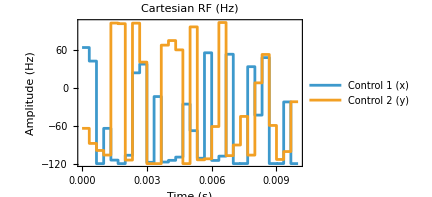
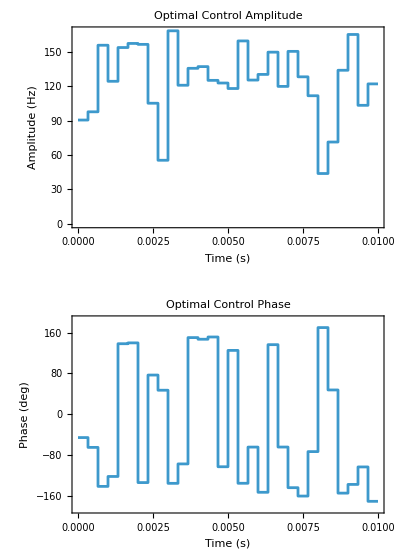
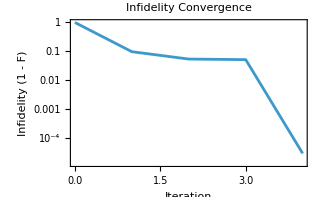
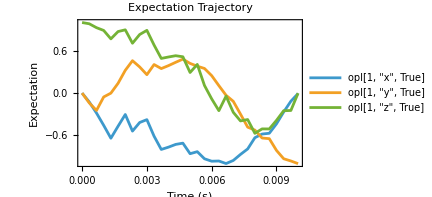
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{{
  PlotOptimalControlWaveform[resGate, PlotLabel -> "Cartesian RF (Hz)", ImageSize -> 320],
  PlotOptimalControlWaveform[resGate, Method -> "AmplitudePhase", ImageSize -> 320]
}, {
  PlotOptimalControlConvergence[resGate, Method -> "Infidelity", ImageSize -> 320],
  PlotOptimalControlTrajectory[resGate, opI[1, "z"], {opI[1, "x"], opI[1, "y"], opI[1, "z"]}, ImageSize -> 320]
}}]
```

## 2. Parameterizations, Regularization, Bounds, Optimizers & Warm Restarts

### 2.1 Smooth Basis Parameterizations, Window Envelopes, Penalties & Box Bounds

Reduce the parameter count and ensure smooth hardware-friendly waveforms using ControlParameterization ("BSpline", "Fourier", "Chebyshev"), ControlWindow -> "Hann", SmoothnessPenalty, PowerPenalty, or asymmetric per-channel ControlBounds.

```mathematica
resBSpline = GRAPEOptimize[
  50. opI[1, "z"], {opI[1, "x"], opI[1, "y"]}, UnitaryTarget[uPi2], {0.01, 40},
  FrequencyUnits -> "Hz", ControlUnits -> "Hz",
  ControlParameterization -> {"BSpline", 12},
  ControlWindow -> "Hann",
  PowerPenalty -> 1.*^-11, SmoothnessPenalty -> 1.*^-10,
  TargetFidelity -> 0.9999, RandomSeed -> 2
];
resFourier = GRAPEOptimize[
  50. opI[1, "z"], {opI[1, "x"], opI[1, "y"]}, UnitaryTarget[uPi2], {0.01, 40},
  FrequencyUnits -> "Hz", ControlUnits -> "Hz",
  ControlParameterization -> {"Fourier", 6}, ControlWindow -> "Hann",
  TargetFidelity -> 0.9999, RandomSeed -> 3
];
resBounds = GRAPEOptimize[
  10. opI[1, "z"], {opI[1, "x"], opI[1, "y"]}, UnitaryTarget[uPi2], {0.02, 20},
  FrequencyUnits -> "Hz", ControlUnits -> "Hz",
  ControlBounds -> {{-40., 40.}, {-25., 35.}},
  MaxIterations -> 60, RandomSeed -> 41
];
<|
  "BSpline" -> {resBSpline["FinalFidelity"], resBSpline["CompiledProblem", "NumParams"]},
  "Fourier" -> {resFourier["FinalFidelity"], resFourier["CompiledProblem", "NumParams"]},
  "BoundsMinMaxCh1" -> MinMax[resBounds["Controls"][[All, 1]]],
  "BoundsMinMaxCh2" -> MinMax[resBounds["Controls"][[All, 2]]],
  "BoundsFidelity" -> resBounds["FinalFidelity"]
|>
```

<|BSpline→{0.999985,12},Fourier→{0.999996,13},BoundsMinMaxCh1→{-40.,-8.64685},BoundsMinMaxCh2→{-24.2745,29.5458},BoundsFidelity→0.999997|>

### 2.2 Optimizer Selection & Grid-Refinement Warm Restarts

Compare Optimizer choices ("LBFGS", "BFGS", "ConjugateGradient") and demonstrate passing a coarse 12-slice OptimalControlResult directly into InitialControls to warm-start a finer 24-slice optimization.

```mathematica
optCompare = Table[
  With[{r = GRAPEOptimize[0, {opI[1, "x"], opI[1, "y"]}, UnitaryTarget[uPi2], {0.01, 10},
      Optimizer -> optName, MaxIterations -> 50, InitialControls -> 20., RandomSeed -> 7]},
    optName -> <|"Fidelity" -> r["FinalFidelity"], "Iterations" -> r["Iterations"]|>
  ],
  {optName, {"LBFGS", "BFGS", "ConjugateGradient"}}
] // Association;

(* Coarse optimization followed by resampled warm restart *)
resCoarse = GRAPEOptimize[10. opI[1, "z"], {opI[1, "x"], opI[1, "y"]}, UnitaryTarget[uPi2],
  {0.01, 12}, FrequencyUnits -> "Hz", ControlUnits -> "Hz", MaxIterations -> 4, InitialScale -> 5., RandomSeed -> 55];
resFine = GRAPEOptimize[10. opI[1, "z"], {opI[1, "x"], opI[1, "y"]}, UnitaryTarget[uPi2],
  {0.01, 24}, FrequencyUnits -> "Hz", ControlUnits -> "Hz", InitialControls -> resCoarse, MaxIterations -> 40];
<|
  "Optimizers" -> optCompare,
  "CoarseFidelity" -> resCoarse["FinalFidelity"],
  "WarmRestartFineFidelity" -> resFine["FinalFidelity"]
|>
```

<|Optimizers→<|LBFGS→<|Fidelity→0.999961,Iterations→3|>,BFGS→<|Fidelity→0.999994,Iterations→4|>,ConjugateGradient→<|Fidelity→0.999997,Iterations→4|>|>,CoarseFidelity→0.999981,WarmRestartFineFidelity→0.999985|>

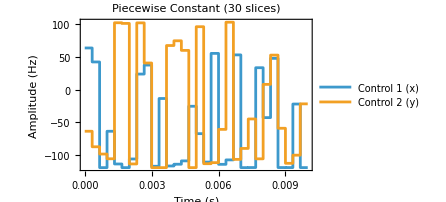
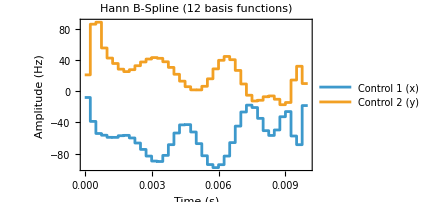

```mathematica
Row[{
  PlotOptimalControlWaveform[resGate, PlotLabel -> "Piecewise Constant (30 slices)", ImageSize -> 330],
  PlotOptimalControlWaveform[resBSpline, PlotLabel -> "Hann B-Spline (12 basis functions)", ImageSize -> 330]
}]
```

## 3. Spin-1 State Transfer & Coupled Two-Spin Quantum Gates (CNOT)

### 3.1 Spin-1 (I = 1, D = 3) State Transfer & Propagation Kernel Comparison

SpinDynamica supports arbitrary spin quantum numbers. Here we transfer |-1> -> |+1> on a spin-1 nucleus (I = 1) with both Zeeman offset and quadrupolar interaction, and compare all propagation/gradient kernels ("Spectral", "BlockMatrixExp", "StateVector", "FirstOrder") via EvaluateOptimalControl.

```mathematica
SetSpinSystem[{{1, 1}}];
bS1 = ZeemanBasis[];
ksS1 = BasisKets[bS1];
resSpin1 = GRAPEOptimize[
  25. opI[1, "z"] + 15. (opI[1, "z"] . opI[1, "z"]),
  {opI[1, "x"], opI[1, "y"]},
  StateTarget[ksS1[[-1]] -> ksS1[[1]], ObjectiveType -> "StateFidelity"],
  {0.02, 30},
  FrequencyUnits -> "Hz", ControlUnits -> "Hz",
  TargetFidelity -> 0.9995, MaxIterations -> 120, RandomSeed -> 3
];

(* Inspect exact agreement across propagation kernels *)
uSample = resSpin1["Controls"];
kernelFids = Table[
  With[{ev = EvaluateOptimalControl[
      CompileOptimalControlProblem[OptimalControlProblem[
        25. opI[1, "z"] + 15. (opI[1, "z"] . opI[1, "z"]),
        {opI[1, "x"], opI[1, "y"]},
        StateTarget[ksS1[[-1]] -> ksS1[[1]]], {0.02, 30},
        FrequencyUnits -> "Hz", ControlUnits -> "Hz", Method -> meth]],
      uSample, True]},
    meth -> <|"Fidelity" -> ev["Fidelity"], "GradNorm" -> Norm[ev["Gradient"]]|>
  ],
  {meth, {"Spectral", "BlockMatrixExp", "StateVector", "FirstOrder"}}
] // Association;
<|"Spin1FinalFidelity" -> resSpin1["FinalFidelity"], "Kernels" -> kernelFids|>
```

SetSpinSystem::set: the spin system has been set to {{1,1}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1}},BasisLabels→Automatic].

<|Spin1FinalFidelity→0.999797,Kernels→<|Spectral→<|Fidelity→0.999797,GradNorm→0.000122656|>,BlockMatrixExp→<|Fidelity→0.999797,GradNorm→0.000122656|>,StateVector→<|Fidelity→0.999797,GradNorm→0.000122656|>,FirstOrder→<|Fidelity→0.999797,GradNorm→0.000120936|>|>|>

### 3.2 Coupled Two-Spin CNOT Gate (4 Control Channels)

Optimize a two-qubit controlled-NOT (CNOT) unitary gate on a J-coupled spin-1/2 pair with independent x/y RF controls on both spins, then verify and plot the multi-channel pulse.

```mathematica
SetSpinSystem[{1, 2}];
b2 = ZeemanBasis[];
uCNOT = {{1., 0., 0., 0.}, {0., 1., 0., 0.}, {0., 0., 0., 1.}, {0., 0., 1., 0.}};
resCNOT = GRAPEOptimize[
  20. opI[1, "z"] - 30. opI[2, "z"] + 140. opI[1, "z"] . opI[2, "z"],
  {opI[1, "x"], opI[1, "y"], opI[2, "x"], opI[2, "y"]},
  UnitaryTarget[uCNOT],
  {0.015, 40},
  FrequencyUnits -> "Hz", ControlUnits -> "Hz",
  TargetFidelity -> 0.9995, MaxIterations -> 150, RandomSeed -> 4
];
simCNOT = VerifyOptimalControlSimulation[resCNOT];
<|
  "CNOT_Fidelity" -> resCNOT["FinalFidelity"],
  "Iterations" -> resCNOT["Iterations"],
  "SDMatch" -> simCNOT["FidelityMatchQ"],
  "PropagatorError" -> simCNOT["PropagatorError"]
|>
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

<|CNOT_Fidelity→0.999534,Iterations→13,SDMatch→True,PropagatorError→4.6257×10^-14|>

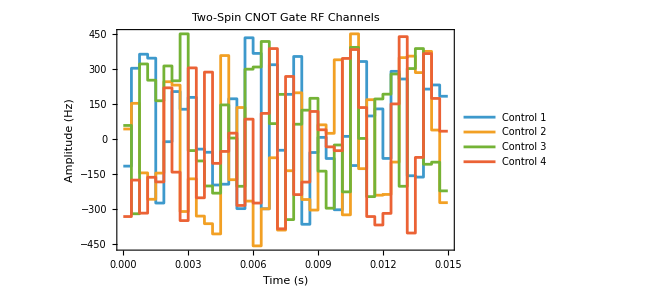

```mathematica
PlotOptimalControlWaveform[resCNOT, PlotLabel -> "Two-Spin CNOT Gate RF Channels", ImageSize -> 480]
```

## 4. NMR Observable Transfer, Non-Hermitian Coherence & Cooperative Pulses

### 4.1 Heteronuclear INEPT Polarization Transfer (ObservableTarget)

Use ObservableTarget to drive selective operator-to-operator transfer I1z -> I2z across a 140 Hz J-coupling. Track the full transfer pathway (I1z -> anti-phase 2 I1z I2z -> I2z) with PlotOptimalControlTrajectory.

```mathematica
SetSpinSystem[{1, 2}];
b2 = ZeemanBasis[];
resInept = GRAPEOptimize[
  30. opI[1, "z"] - 45. opI[2, "z"] + 140. opI[1, "z"] . opI[2, "z"],
  {opI[1, "x"], opI[1, "y"], opI[2, "x"], opI[2, "y"]},
  ObservableTarget[opI[1, "z"] -> opI[2, "z"]],
  {0.015, 40},
  FrequencyUnits -> "Hz", ControlUnits -> "Hz",
  TargetFidelity -> 0.9995, MaxIterations -> 150, RandomSeed -> 11
];
simInept = VerifyOptimalControlSimulation[resInept];
<|"INEPT_Fidelity" -> resInept["FinalFidelity"], "SDMatch" -> simInept["FidelityMatchQ"]|>
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

<|INEPT_Fidelity→0.999924,SDMatch→True|>

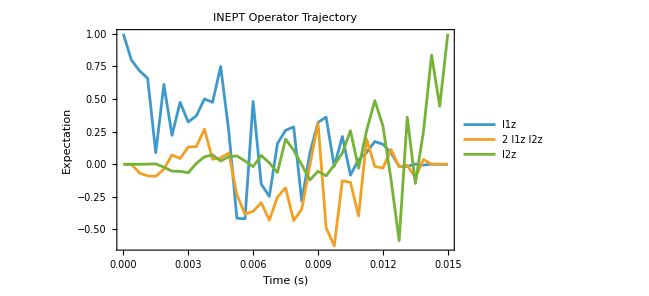

```mathematica
PlotOptimalControlTrajectory[resInept, opI[1, "z"], {opI[1, "z"], 2 opI[1, "z"] . opI[2, "z"], opI[2, "z"]}, PlotLegends -> {"I1z", "2 I1z I2z", "I2z"}, PlotLabel -> "INEPT Operator Trajectory", ImageSize -> 480]
```

### 4.2 Non-Hermitian Coherence-Order Transfer (CoherenceTarget)

CoherenceTarget supports non-Hermitian spin raising/lowering operators, either phase-sensitive (PhaseInsensitive -> False) or phase-insensitive (PhaseInsensitive -> True), with configurable TargetNormalization ("Frobenius", "TargetNorm", "None").

```mathematica
resCoh = GRAPEOptimize[
  25. opI[1, "z"] - 35. opI[2, "z"] + 140. opI[1, "z"] . opI[2, "z"],
  {opI[1, "x"], opI[1, "y"], opI[2, "x"], opI[2, "y"]},
  CoherenceTarget[opI[1, "+"] . opI[2, "-"] -> opI[1, "+"] . opI[2, "+"],
    PhaseInsensitive -> True, TargetNormalization -> "Frobenius"],
  {0.015, 36},
  FrequencyUnits -> "Hz", ControlUnits -> "Hz",
  TargetFidelity -> 0.995, MaxIterations -> 160, RandomSeed -> 15
];
<|"ZQ_to_DQ_Fidelity" -> resCoh["FinalFidelity"], "Iterations" -> resCoh["Iterations"]|>
```

<|ZQ_to_DQ_Fidelity→0.996344,Iterations→6|>

### 4.3 Cooperative Objectives (Universal Point-to-Point Rotation)

CooperativeObjective simultaneously optimizes a single waveform across multiple initial->target pairs with optional weights (controlled via NormalizeWeights -> True | False). Below we synthesize a universal pi_x pulse by driving Ix -> Ix, Iy -> -Iy, and Iz -> -Iz simultaneously, then cross-check with TransformationAmplitude.

```mathematica
SetSpinSystem[1];
b1 = ZeemanBasis[];
resCoop = GRAPEOptimize[
  40. opI[1, "z"], {opI[1, "x"], opI[1, "y"]},
  CooperativeObjective[{
    {2., opI[1, "z"] -> -opI[1, "z"]},
    {1., opI[1, "x"] -> opI[1, "x"]},
    {1., opI[1, "y"] -> -opI[1, "y"]}
  }, NormalizeWeights -> True],
  {0.01, 24},
  FrequencyUnits -> "Hz", ControlUnits -> "Hz",
  TargetFidelity -> 0.9995, MaxIterations -> 80, RandomSeed -> 33
];
simCoop = VerifyOptimalControlSimulation[resCoop];
taCheck = Re[N[TransformationAmplitude[opI[1, "z"] -> -opI[1, "z"], OptimalControlEventList[resCoop]]]];
<|
  "CooperativeFidelity" -> resCoop["FinalFidelity"],
  "IzToMinusIz_TransformationAmplitude" -> taCheck,
  "SDMatch" -> simCoop["FidelityMatchQ"]
|>
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

<|CooperativeFidelity→0.999988,IzToMinusIz_TransformationAmplitude→0.999995,SDMatch→True|>

## 5. Open-System (Dissipative Liouville-Space) Optimal Control

When the drift contains a Superoperator such as PhenomenologicalRelaxationSuperoperator or Lindbladian (or when PropagateSpace -> "Liouville" is requested), OptimalControl automatically switches to exact Liouville-space propagation and adjoint gradients, verified directly against SpinDynamica superpropagators.

```mathematica
SetSpinSystem[1];
gRel = PhenomenologicalRelaxationSuperoperator[1, 1.5];
probLiouv = OptimalControlProblem[
  gRel + (-I CommutationSuperoperator[5. opI[1, "z"]]),
  {opI[1, "x"], opI[1, "y"]},
  ObservableTarget[opI[1, "z"] -> opI[1, "x"]],
  {0.01, 16},
  PropagateSpace -> "Liouville"
];
chkLiouvGrad = VerifyOptimalControlGradient[probLiouv, ConstantArray[{25., -15.}, 16]];
resLiouv = GRAPEOptimize[probLiouv, MaxIterations -> 50, InitialControls -> 5., RandomSeed -> 3];
simLiouv = VerifyOptimalControlSimulation[resLiouv];
<|
  "PropagateSpace" -> resLiouv["CompiledProblem", "Space"],
  "GradientPassedQ" -> chkLiouvGrad["PassedQ"],
  "DissipativeTransfer" -> resLiouv["FinalFidelity"],
  "SDMatch" -> simLiouv["FidelityMatchQ"],
  "FidelityError" -> simLiouv["FidelityError"]
|>
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

<|PropagateSpace→Liouville,GradientPassedQ→True,DissipativeTransfer→0.993141,SDMatch→True,FidelityError→3.33067×10^-16|>

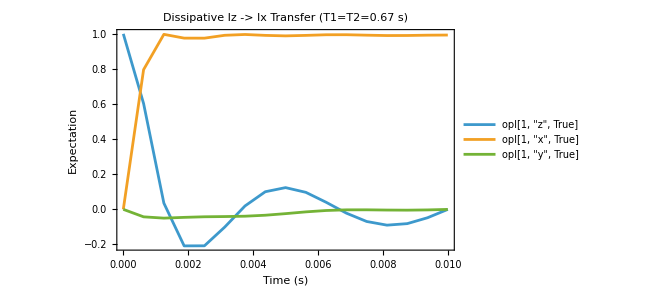

```mathematica
PlotOptimalControlTrajectory[resLiouv, opI[1, "z"], {opI[1, "z"], opI[1, "x"], opI[1, "y"]}, PlotLabel -> "Dissipative Iz -> Ix Transfer (T1=T2=0.67 s)", ImageSize -> 480]
```

## 6. Robust & Cooperative Ensemble Optimal Control

### 6.1 Broadband Offset Compensation ("Mean" vs "SoftMin")

Use OptimalControlEnsemble with EnsembleParameters to design pulses robust against resonance offsets delta in [-5, +5] kHz. Affine parameter terms are automatically hoisted and evaluated fast across all ensemble members. Compare average maximization ("Mean") vs worst-case smoothing ({"SoftMin", beta}), inspect EvaluateEnsembleFidelity, and plot the profile.

```mathematica
SetSpinSystem[1];
b1 = ZeemanBasis[];
ks1 = BasisKets[b1];
ensMean = OptimalControlEnsemble[
  delta opI[1, "z"], {opI[1, "x"], opI[1, "y"]}, StateTarget[ks1[[1]] -> ks1[[2]]], {0.002, 30},
  FrequencyUnits -> "kHz", ControlUnits -> "kHz",
  EnsembleParameters -> {delta -> Range[-5., 5., 1.]},
  EnsembleAggregation -> "Mean"
];
ensSoft = OptimalControlEnsemble[
  delta opI[1, "z"], {opI[1, "x"], opI[1, "y"]}, StateTarget[ks1[[1]] -> ks1[[2]]], {0.002, 30},
  FrequencyUnits -> "kHz", ControlUnits -> "kHz",
  EnsembleParameters -> {delta -> Range[-5., 5., 1.]},
  EnsembleAggregation -> {"SoftMin", 20.}
];
resMean = GRAPEOptimize[ensMean, AmplitudeBound -> 8., TargetFidelity -> 0.996, MaxIterations -> 120, RandomSeed -> 101];
resSoft = GRAPEOptimize[ensSoft, AmplitudeBound -> 8., TargetFidelity -> 0.996, MaxIterations -> 120, RandomSeed -> 101];
simMean = VerifyOptimalControlSimulation[resMean];
evalMean = EvaluateEnsembleFidelity[resMean];
evalSoft = EvaluateEnsembleFidelity[resSoft];
<|
  "MeanAggregation" -> <|"Mean" -> evalMean["MeanFidelity"], "Min" -> evalMean["MinFidelity"], "SDMatch" -> simMean["FidelityMatchQ"]|>,
  "SoftMinAggregation" -> <|"Mean" -> evalSoft["MeanFidelity"], "Min" -> evalSoft["MinFidelity"]|>
|>
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

<|MeanAggregation→<|Mean→0.997476,Min→0.994324,SDMatch→True|>,SoftMinAggregation→<|Mean→0.997206,Min→0.992196|>|>

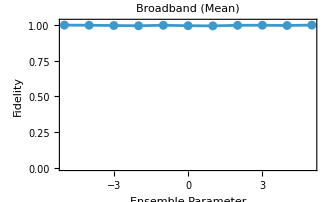
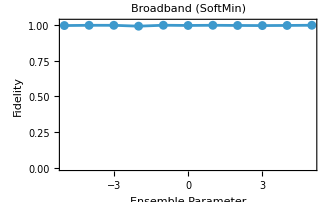

```mathematica
Row[{PlotEnsembleFidelity[evalMean, PlotLabel -> "Broadband (Mean)", ImageSize -> 330], PlotEnsembleFidelity[evalSoft, PlotLabel -> "Broadband (SoftMin)", ImageSize -> 330]}]
```

### 6.2 2D Offset x RF Inhomogeneity & J-Compensated NMR Ensembles

Combine EnsembleParameters with RFInhomogeneity -> {0.8, ..., 1.2} for two-dimensional robustness maps, and build J-compensated two-spin transfers (optionally setting Parallel -> 2 for multi-kernel speedups).

```mathematica
ens2D = OptimalControlEnsemble[
  delta opI[1, "z"], {opI[1, "x"], opI[1, "y"]}, StateTarget[ks1[[1]] -> ks1[[2]]], {0.002, 32},
  FrequencyUnits -> "kHz", ControlUnits -> "kHz",
  EnsembleParameters -> {delta -> Range[-2.5, 2.5, 1.25]},
  RFInhomogeneity -> {0.8, 0.9, 1.0, 1.1, 1.2},
  EnsembleAggregation -> {"SoftMin", 15.}
];
res2D = GRAPEOptimize[ens2D, AmplitudeBound -> 8., TargetFidelity -> 0.995, MaxIterations -> 140, RandomSeed -> 202];

(* J-compensated 2-spin INEPT across J in [120, 160] Hz (set Parallel -> 2 for multi-kernel) *)
SetSpinSystem[{1, 2}];
ensJ = OptimalControlEnsemble[
  jVal opI[1, "z"] . opI[2, "z"], {opI[1, "x"], opI[1, "y"], opI[2, "x"], opI[2, "y"]},
  ObservableTarget[opI[1, "z"] -> opI[2, "z"]], {0.015, 40},
  FrequencyUnits -> "Hz", ControlUnits -> "Hz",
  EnsembleParameters -> {jVal -> {120., 130., 140., 150., 160.}}
];
resJ = GRAPEOptimize[ensJ, TargetFidelity -> 0.996, MaxIterations -> 150, RandomSeed -> 303];
<|
  "2D_GridShape" -> res2D["GridShape"],
  "2D_MeanFidelity" -> res2D["MeanMemberFidelity"],
  "2D_MinFidelity" -> res2D["MinMemberFidelity"],
  "JRobust_MeanFidelity" -> resJ["MeanMemberFidelity"],
  "JRobust_MinFidelity" -> resJ["MinMemberFidelity"]
|>
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

<|2D_GridShape→{5,5},2D_MeanFidelity→0.995333,2D_MinFidelity→0.976372,JRobust_MeanFidelity→0.99615,JRobust_MinFidelity→0.989284|>

```mathematica
PlotEnsembleFidelity[res2D, PlotLabel -> "2D Offset x RF Inhomogeneity Fidelity", ImageSize -> 420]
```

-Graphics-

### 6.3 Nonlinear Powder Grids & Heterogeneous Spin Ensembles

Weighted nonlinear Hamiltonians (such as second-rank Legendre CSA powder grids weighted by Sin[beta]) and OptimalControlEnsemble[{prob1, prob2}] combining different spin systems or objectives fall back seamlessly to exact numerical evaluation.

```mathematica
SetSpinSystem[1];
betaGrid = Table[{beta, N[Sin[beta]]}, {beta, Pi/8, 7 Pi/8, Pi/4}];
ensPowder = OptimalControlEnsemble[
  0.5 (3 Cos[beta]^2 - 1.) opI[1, "z"] + 0.3 Sin[beta] opI[1, "x"],
  {opI[1, "x"], opI[1, "y"]},
  ObservableTarget[opI[1, "z"] -> -opI[1, "z"]],
  {0.002, 20}, FrequencyUnits -> "kHz", ControlUnits -> "kHz",
  EnsembleParameters -> {beta -> betaGrid}
];
resPowder = GRAPEOptimize[ensPowder, AmplitudeBound -> 8., MaxIterations -> 100, RandomSeed -> 404];
simPowder = VerifyOptimalControlSimulation[resPowder];
<|"PowderMean" -> resPowder["MeanMemberFidelity"], "PowderMin" -> resPowder["MinMemberFidelity"], "SDMatch" -> simPowder["FidelityMatchQ"]|>
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

<|PowderMean→0.999999,PowderMin→0.999999,SDMatch→True|>

## 7. Exporting Optimal Pulses into Native SpinDynamica Workflows

### 7.1 OptimalControlWaveform, OptimalControlEventList, Trajectory & Signal1D

Every OptimalControlResult exports seamlessly to native SpinDynamica building blocks: OptimalControlWaveform returns structured slice arrays, while OptimalControlEventList produces {{H_j, dt_j}, ...} ready for NPropagationOperator, NPropagate, Trajectory, and Signal1D Preparation.

```mathematica
wf = OptimalControlWaveform[resGate];
evGate = OptimalControlEventList[resGate];
SetSpinSystem[1]; b1 = ZeemanBasis[];
uSD = Normal[MatrixRepresentation[NPropagationOperator[evGate, Basis -> b1], b1]];
trajGate = Trajectory[opI[1, "z"] -> {opI[1, "x"], opI[1, "y"], opI[1, "z"]}, evGate];

(* Use the optimal (pi/2)_x pulse as Preparation for a 1D NMR FID *)
sigOC = Signal1D[{0, 0.1, 0.0005}, 2 Pi 120. opI[1, "z"],
  Preparation -> evGate,
  InitialDensityOperator -> opI[1, "z"],
  Observable -> 1,
  ReportSignalCalculationMethod -> False
];
<|
  "WaveformKeys" -> Keys[wf],
  "NumEvents" -> Length[evGate],
  "PropagatorDiff" -> Max[Abs[uSD - resGate["FinalPropagator"]]],
  "EndBlochVector" -> Chop[Through[trajGate[0.01]]],
  "SignalHead" -> Head[sigOC]
|>
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

Signal1D::droplast: the last sampling point has been dropped in order to get an even number of points.

Signal1D::autolb: Using LineBroadening → 2π × 14.6587 rad s^-1.

<|WaveformKeys→{Controls,Parameters,TimeSteps,TimeEdges,TimeMidpoints,Duration,InitialTimePoint,DriftIntegration,Drift,ChannelOperators,DriftUnitFactor,ControlUnitFactor,FrequencyUnits,ControlUnits,Space,Basis,OperatorBasis},NumEvents→30,PropagatorDiff→1.45028×10^-15,EndBlochVector→{-0.00621019,-0.99998,-0.00112395},SignalHead→Signal|>

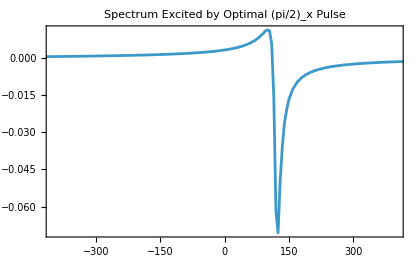

```mathematica
ListPlot[Re[FT[sigOC]], Frame -> True, Joined -> True, PlotRange -> {{-400, 400}, All}, PlotLabel -> "Spectrum Excited by Optimal (pi/2)_x Pulse", ImageSize -> 420]
```

### 7.2 Order-0 Generators (OptimalControlGenerator) & ShapedPulse Sequences (OptimalControlPulseSequence)

Export pulses either as a piecewise-constant TimeDependentGeneratorFunction via OptimalControlGenerator[res, t], or (for homonuclear/single-spin XY controls) as a SpinDynamica PulseSequence[ShapedPulse[...]] via OptimalControlPulseSequence.

```mathematica
SetSpinSystem[{1, 2}]; b2 = ZeemanBasis[];
genInept = OptimalControlGenerator[resInept, tGlobal];
uGen = Normal[MatrixRepresentation[NPropagationOperator[{genInept, 0.015}, Basis -> b2], b2]];

(* Homonuclear 2-spin transfer exported as a PulseSequence with ShapedPulse *)
resHomo = GRAPEOptimize[
  120. opI[1, "z"] - 80. opI[2, "z"] + 60. opI[1, "z"] . opI[2, "z"],
  {opI[1, "x"] + opI[2, "x"], opI[1, "y"] + opI[2, "y"]},
  ObservableTarget[opI[1, "z"] -> opI[2, "z"]],
  {0.02, 30}, FrequencyUnits -> "Hz", ControlUnits -> "Hz",
  TargetFidelity -> 0.995, MaxIterations -> 120, RandomSeed -> 14
];
psHomo = OptimalControlPulseSequence[resHomo, {1, 2}];
<|
  "GeneratorHead" -> Head[genInept],
  "GeneratorPropagatorError" -> Max[Abs[uGen - resInept["FinalPropagator"]]],
  "HomoFidelity" -> resHomo["FinalFidelity"],
  "PulseSequenceHead" -> Head[psHomo],
  "ContainsShapedPulseQ" -> !FreeQ[psHomo, ShapedPulse]
|>
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

<|GeneratorHead→TimeDependentGeneratorFunction,GeneratorPropagatorError→3.27186×10^-14,HomoFidelity→0.997729,PulseSequenceHead→PulseSequence,ContainsShapedPulseQ→True|>

## 8. Strong-Wolfe Line Search, Physical RF Constraints, FISTA & Continuation (Phase 1)

### 8.1 Strong-Wolfe vs Armijo, Polar RF Disk (AmplitudeNormBound) & SlewRateBound

Phase 1 upgrades unconstrained L-BFGS / BFGS / ConjugateGradient to a safeguarded Strong-Wolfe line search (with projected Armijo fallback when bounds are active) and introduces true polar RF disk limits via AmplitudeNormBound (Sqrt[ux^2 + uy^2] <= wMax, eliminating the Sqrt[2] Cartesian box corner overshoot) alongside discrete-time derivative limits SlewRateBound.

```mathematica
SetSpinSystem[1]; b1 = ZeemanBasis[];
uPi2 = MatrixExp[-I (Pi / 2.) Normal[MatrixRepresentation[opI[1, "x"], b1]]];
probP1 = OptimalControlProblem[80. opI[1, "z"], {opI[1, "x"], opI[1, "y"]}, UnitaryTarget[uPi2], {0.01, 24}, FrequencyUnits -> "Hz", ControlUnits -> "Hz"];

resSW = GRAPEOptimize[probP1, LineSearch -> "StrongWolfe", TargetFidelity -> 0.9999, MaxIterations -> 80, RandomSeed -> 11];
resArm = GRAPEOptimize[probP1, LineSearch -> "Armijo", TargetFidelity -> 0.9999, MaxIterations -> 80, RandomSeed -> 11];
resBox85 = GRAPEOptimize[probP1, AmplitudeBound -> 85., TargetFidelity -> 0.9995, MaxIterations -> 100, RandomSeed -> 5];
resDisk85 = GRAPEOptimize[probP1, AmplitudeNormBound -> 85., TargetFidelity -> 0.9995, MaxIterations -> 120, RandomSeed -> 5];
resSlew18 = GRAPEOptimize[50. opI[1, "z"], {opI[1, "x"], opI[1, "y"]}, UnitaryTarget[uPi2], {0.015, 30},
  FrequencyUnits -> "Hz", ControlUnits -> "Hz", AmplitudeNormBound -> 90., SlewRateBound -> 18000., TargetFidelity -> 0.999, MaxIterations -> 140, RandomSeed -> 9];

(* Heteronuclear channel-pair disk bounds on a 2-spin INEPT transfer *)
SetSpinSystem[{1, 2}];
resHetDisk = GRAPEOptimize[30. opI[1, "z"] - 45. opI[2, "z"] + 140. opI[1, "z"] . opI[2, "z"],
  {opI[1, "x"], opI[1, "y"], opI[2, "x"], opI[2, "y"]}, ObservableTarget[opI[1, "z"] -> opI[2, "z"]], {0.015, 40},
  FrequencyUnits -> "Hz", ControlUnits -> "Hz", AmplitudeNormBound -> {{1, 2} -> 120., {3, 4} -> 180.}, TargetFidelity -> 0.999, MaxIterations -> 150, RandomSeed -> 11];
simHetDisk = VerifyOptimalControlSimulation[resHetDisk];
<|
  "StrongWolfe" -> {resSW["FinalFidelity"], resSW["Evaluations"], resSW["LineSearchMethod"]},
  "Armijo" -> {resArm["FinalFidelity"], resArm["Evaluations"], resArm["LineSearchMethod"]},
  "Box85_MaxRadiusHz" -> Max[Sqrt[Total[resBox85["Controls"]^2, {2}]]],
  "Disk85_MaxRadiusHz" -> Max[Sqrt[Total[resDisk85["Controls"]^2, {2}]]],
  "Disk85_Viol" -> resDisk85["MaxConstraintViolation"],
  "DiskSlew_F" -> resSlew18["FinalFidelity"],
  "DiskSlew_MaxRate" -> Max[Abs[Differences[resSlew18["Controls"]]] / (0.015 / 30.)],
  "HetDisk_F" -> resHetDisk["FinalFidelity"],
  "HetDisk_SDMatch" -> simHetDisk["FidelityMatchQ"]
|>
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

<|StrongWolfe→{0.999994,7,StrongWolfe},Armijo→{0.999994,8,Armijo},Box85_MaxRadiusHz→120.208,Disk85_MaxRadiusHz→85.,Disk85_Viol→1.42109×10^-14,DiskSlew_F→0.999623,DiskSlew_MaxRate→18000.,HetDisk_F→0.999733,HetDisk_SDMatch→True|>

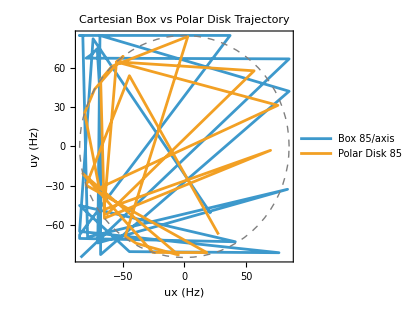
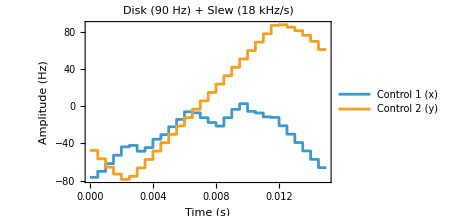

```mathematica
Row[{
  ListPlot[{resBox85["Controls"], resDisk85["Controls"]}, Joined -> True, AspectRatio -> 1,
    PlotLegends -> {"Box 85/axis", "Polar Disk 85"},
    Epilog -> {Dashed, Gray, Circle[{0, 0}, 85.]}, Frame -> True, FrameLabel -> {"ux (Hz)", "uy (Hz)"},
    PlotLabel -> "Cartesian Box vs Polar Disk Trajectory", ImageSize -> 310],
  PlotOptimalControlWaveform[resSlew18, PlotLabel -> "Disk (90 Hz) + Slew (18 kHz/s)", ImageSize -> 350]
}]
```

### 8.2 Sparse & Piecewise-Constant Pulses via FISTA (L1Penalty, TVPenalty) & Q-Space ADMM

Adding L1Penalty or TVPenalty (using Condat's exact O(N_t) total-variation proximal operator) or combining waveform constraints with parameterized bases (Fourier / B-spline via thin-SVD orthonormal Q-space reduction) automatically engages monotone-safeguarded adaptive-restart FISTA.

```mathematica
SetSpinSystem[1]; b1 = ZeemanBasis[];
resUnreg = GRAPEOptimize[20. opI[1, "z"], {opI[1, "x"], opI[1, "y"]}, UnitaryTarget[uPi2], {0.02, 40},
  FrequencyUnits -> "Hz", ControlUnits -> "Hz", AmplitudeNormBound -> 90., Optimizer -> "FISTA", TargetFidelity -> 0.995, MaxIterations -> 140, RandomSeed -> 31];
resL1TV = GRAPEOptimize[20. opI[1, "z"], {opI[1, "x"], opI[1, "y"]}, UnitaryTarget[uPi2], {0.02, 40},
  FrequencyUnits -> "Hz", ControlUnits -> "Hz", AmplitudeNormBound -> 90., L1Penalty -> 1.*^-4, TVPenalty -> 2.*^-4, MaxIterations -> 180, RandomSeed -> 31];
resHannBSplineSlew = GRAPEOptimize[50. opI[1, "z"], {opI[1, "x"], opI[1, "y"]}, UnitaryTarget[uPi2], {0.01, 32},
  FrequencyUnits -> "Hz", ControlUnits -> "Hz", ControlParameterization -> {"BSpline", 12}, ControlWindow -> "Hann",
  AmplitudeNormBound -> 120., SlewRateBound -> 40000., MaxIterations -> 150, RandomSeed -> 22];
<|
  "Unreg_F" -> resUnreg["FinalFidelity"],
  "Unreg_TV" -> Total[Abs[Flatten[Differences[resUnreg["Controls"]]]]],
  "L1TV_F" -> resL1TV["FinalFidelity"],
  "L1TV_TV" -> Total[Abs[Flatten[Differences[resL1TV["Controls"]]]]],
  "L1TV_Optimizer" -> resL1TV["Optimizer"],
  "BSplineSlew_F" -> resHannBSplineSlew["FinalFidelity"],
  "BSplineSlew_Viol" -> resHannBSplineSlew["MaxConstraintViolation"]
|>
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2}},BasisLabels→Automatic].

<|Unreg_F→0.999697,Unreg_TV→4220.94,L1TV_F→0.995816,L1TV_TV→117.065,L1TV_Optimizer→FISTA,BSplineSlew_F→0.999967,BSplineSlew_Viol→1.13687×10^-13|>

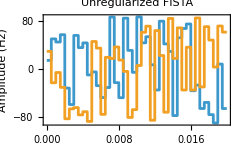
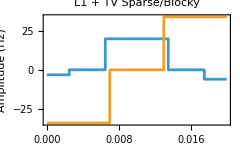
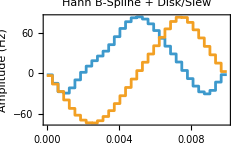

```mathematica
Row[{
  PlotOptimalControlWaveform[resUnreg, PlotLabel -> "Unregularized FISTA", ImageSize -> 240],
  PlotOptimalControlWaveform[resL1TV, PlotLabel -> "L1 + TV Sparse/Blocky", ImageSize -> 240],
  PlotOptimalControlWaveform[resHannBSplineSlew, PlotLabel -> "Hann B-Spline + Disk/Slew", ImageSize -> 240]
}]
```

### 8.3 Continuation Schedules (TimeStepSchedule, SoftMinSchedule), MultiStart & Live StepMonitor

Combine coarse-to-fine TimeStepSchedule, SoftMinSchedule beta annealing, MultiStart (with deterministic BlockRandom seeds), and non-intrusive outer-iteration StepMonitor callbacks on a 27-member 2D Offset x RF Inhomogeneity ensemble.

```mathematica
SetSpinSystem[1]; b1 = ZeemanBasis[]; ks1 = BasisKets[b1];
ensBBCont = OptimalControlEnsemble[
  delta opI[1, "z"], {opI[1, "x"], opI[1, "y"]}, StateTarget[ks1[[1]] -> ks1[[2]]], 0.002,
  FrequencyUnits -> "kHz", ControlUnits -> "kHz",
  EnsembleParameters -> {delta -> Range[-5., 5., 1.25]},
  RFInhomogeneity -> {0.85, 1.0, 1.15},
  EnsembleAggregation -> {"SoftMin", 25.}
];
monLog = {};
resCont = GRAPEOptimize[
  ensBBCont, AmplitudeNormBound -> 8.,
  TimeStepSchedule -> {16, 32}, SoftMinSchedule -> {0., 8., 25.}, MultiStart -> 3, MaxIterations -> 90,
  StepMonitor -> (AppendTo[monLog, #] &), MonitorInterval -> 20, RandomSeed -> 77
];
simCont = VerifyOptimalControlSimulation[resCont];
<|
  "MeanF" -> resCont["MeanMemberFidelity"],
  "MinF" -> resCont["MinMemberFidelity"],
  "FinalSlices" -> Length[resCont["TimeSteps"]],
  "Stages" -> Length[resCont["ContinuationHistory"]],
  "MultiStarts" -> Length[resCont["MultiStartResults"]],
  "MonitorEvents" -> Length[monLog],
  "SDMatch" -> simCont["FidelityMatchQ"]
|>
```

SetSpinSystem::set: the spin system has been set to {{1,1/2}}

<|MeanF→0.999798,MinF→0.999188,FinalSlices→32,Stages→4,MultiStarts→3,MonitorEvents→42,SDMatch→True|>

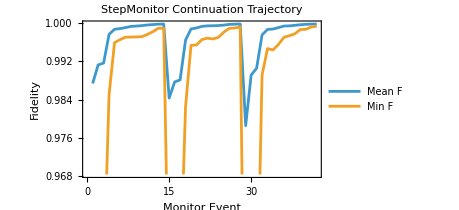
-Graphics--Graphics-

```mathematica
Row[{
  PlotEnsembleFidelity[resCont, PlotLabel -> "2D Robust Ensemble (Fmin = " <> ToString[Round[resCont["MinMemberFidelity"], 0.0001]] <> ")", ImageSize -> 340],
  ListLinePlot[{#["MeanFidelity"] & /@ monLog, #["MinFidelity"] & /@ monLog},
    PlotLegends -> {"Mean F", "Min F"}, Frame -> True, FrameLabel -> {"Monitor Event", "Fidelity"},
    PlotLabel -> "StepMonitor Continuation Trajectory", ImageSize -> 340]
}]
```

## 9. Solid-State / MAS Time-Dependent Drift Hamiltonians (Phase 2A)

### 9.1 Continuous MAS Drift, InitialTimePoint & DriftIntegration Schemes (CF4 / SubSlices)

Phase 2A extends OptimalControlProblem and OptimalControlEnsemble to continuously time-dependent and periodic Hamiltonians such as Magic-Angle Spinning (MAS) PeriodicFunction / TimeDependentGeneratorFunction drifts, with exact InitialTimePoint rotor-phase control and 4th-order commutator-free Magnus integration ("CF4" / {"CF4", q}).

```mathematica
SetSpinSystem[{{1, 1/2}, {2, 1/2}}]; b2 = ZeemanBasis[];
ctrls4 = {opI[1, "x"], opI[1, "y"], opI[2, "x"], opI[2, "y"]};
trMAS = 1. / 10000.; wr = 2. Pi / trMAS;
Hdip = PeriodicFunction[t, trMAS, Evaluate[
  1500. * opI[1, "z"] - 3500. * opI[2, "z"] +
  4000. * Cos[wr t] * opI[1, "z"] +
  6000. * (Cos[wr t] + 0.5 Sin[2 wr t]) * (2 opI[1, "z"] . opI[2, "z"] - opI[1, "x"] . opI[2, "x"] - opI[1, "y"] . opI[2, "y"])
]];
SeedRandom[901]; uProbe = RandomReal[{-3000., 3000.}, {12, 4}];
propsMAS = Table[
  scheme -> EvaluateOptimalControl[
    CompileOptimalControlProblem[OptimalControlProblem[Hdip, ctrls4, StateTarget[opI[1, "z"] -> opI[2, "z"]],
      {2. * trMAS, 12}, FrequencyUnits -> "Hz", InitialTimePoint -> trMAS / 4., DriftIntegration -> scheme]],
    uProbe, True]["FinalPropagator"],
  {scheme, {"Midpoint", {"SubSlices", 4}, "CF4", {"CF4", 2}, {"CF4", 4}}}
] // Association;
uRefCF44 = propsMAS[{"CF4", 4}];
vgMAS = VerifyOptimalControlGradient[
  OptimalControlProblem[Hdip, ctrls4, StateTarget[opI[1, "z"] -> opI[2, "z"]], {2. * trMAS, 12}, FrequencyUnits -> "Hz", InitialTimePoint -> trMAS / 4., DriftIntegration -> "CF4"],
  uProbe, StepSize -> 0.5];
<|
  "DiffVsCF4x4" -> <|"Midpoint" -> Max[Abs[propsMAS["Midpoint"] - uRefCF44]],
    "SubSlices4" -> Max[Abs[propsMAS[{"SubSlices", 4}] - uRefCF44]],
    "CF4" -> Max[Abs[propsMAS["CF4"] - uRefCF44]],
    "CF4x2" -> Max[Abs[propsMAS[{"CF4", 2}] - uRefCF44]]|>,
  "CF4_GradRelErr" -> vgMAS["MaxRelativeError"]
|>
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

SetBasis::set: the state basis has been set to ZeemanBasis[{{1,1/2},{2,1/2}},BasisLabels→Automatic].

<|DiffVsCF4x4→<|Midpoint→0.0470929,SubSlices4→0.00273648,CF4→0.00139787,CF4x2→0.0000591253|>,CF4_GradRelErr→5.81544×10^-10|>

### 9.2 Rotor-Phase Invariant MAS Recoupling & Signal1D COMPUTE Verification

Sweep InitialTimePoint across rotor phases via EnsembleParameters to design a gamma/rotor-phase-invariant I1z -> I2z recoupling pulse over two rotor periods, verify it against NPropagationOperator via VerifyOptimalControlSimulation, and cross-check follow-up MAS Signal1D acquisition under SignalCalculationMethod -> "COMPUTE" vs "Direct".

```mathematica
ensMAS = OptimalControlEnsemble[
  Hdip, ctrls4, StateTarget[opI[1, "z"] -> opI[2, "z"]], {2. * trMAS, 24},
  EnsembleParameters -> {t0Sym -> {0., trMAS / 4., trMAS / 2., 3. * trMAS / 4.}},
  InitialTimePoint -> t0Sym, FrequencyUnits -> "Hz", ControlUnits -> "Hz", DriftIntegration -> {"CF4", 2}
];
resMAS = GRAPEOptimize[ensMAS, AmplitudeNormBound -> 18000., MaxIterations -> 140, TargetFidelity -> 0.995, RandomSeed -> 77];
simMAS = VerifyOptimalControlSimulation[resMAS, Tolerance -> 10^-5];
rhoAfterMAS = NPropagate[
  OptimalControlEventList[resMAS, IncludeDrift -> False, Chronology -> "LeftToRight"],
  Basis -> b2, Chronology -> "LeftToRight", BackgroundGenerator -> Hdip, InitialTimePoint -> 0.
][opI[1, "z"]];
sigMASComp = Quiet[Signal1D[{0, 3 trMAS, trMAS / 4.}, {None, 3 trMAS},
  InitialDensityOperator -> rhoAfterMAS, Observable -> opI[2, "z"],
  BackgroundGenerator -> Hdip, InitialTimePoint -> 2. * trMAS,
  SignalCalculationMethod -> "COMPUTE", LineBroadening -> None, DigitalFrequencyResolution -> False, ReportSignalCalculationMethod -> False]];
sigMASDir = Quiet[Signal1D[{0, 3 trMAS, trMAS / 4.}, {None, 3 trMAS},
  InitialDensityOperator -> rhoAfterMAS, Observable -> opI[2, "z"],
  BackgroundGenerator -> Hdip, InitialTimePoint -> 2. * trMAS,
  SignalCalculationMethod -> "Direct", LineBroadening -> None, ReportSignalCalculationMethod -> False]];
<|
  "MAS_MeanF" -> resMAS["MeanMemberFidelity"],
  "MAS_MinF" -> resMAS["MinMemberFidelity"],
  "MAS_SDMatch" -> simMAS["FidelityMatchQ"],
  "Signal1D_ComputeVsDirectErr" -> Max[Abs[(Last /@ Expand[sigMASComp]) - (Last /@ Expand[sigMASDir])]]
|>
```

<|MAS_MeanF→0.995064,MAS_MinF→0.993588,MAS_SDMatch→True,Signal1D_ComputeVsDirectErr→2.4515×10^-8|>

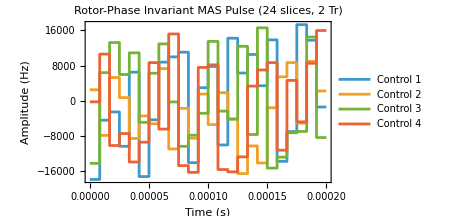
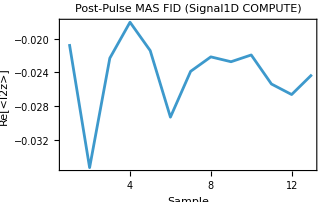

```mathematica
Row[{
  PlotOptimalControlWaveform[resMAS, PlotLabel -> "Rotor-Phase Invariant MAS Pulse (24 slices, 2 Tr)", ImageSize -> 350],
  ListPlot[Re[Last /@ Expand[sigMASComp]], Joined -> True, Frame -> True, FrameLabel -> {"Sample", "Re[<I2z>]"},
    PlotLabel -> "Post-Pulse MAS FID (Signal1D COMPUTE)", ImageSize -> 330]
}]
```

## 10. Trajectory Running Costs & Slice Duration Optimization (Phase 2B)

### 10.1 Forbidden Intermediate-State Suppression (RunningCost & StatePenalty)

RunningCost -> StatePenalty[...] evaluates intermediate state populations or expectation values at every slice boundary and injects exact adjoint boundary costates. Below we steer |alpha,alpha> -> |beta,beta> while suppressing the forbidden |alpha,beta> state by >10^5-fold without sacrificing terminal fidelity.

```mathematica
SetSpinSystem[{{1, 1/2}, {2, 1/2}}]; b2 = ZeemanBasis[]; ks2 = BasisKets[b2];
psi1 = N[Flatten[Normal[MatrixRepresentation[ks2[[1]], b2]]]];
psi2 = N[Flatten[Normal[MatrixRepresentation[ks2[[2]], b2]]]];
psi4 = N[Flatten[Normal[MatrixRepresentation[ks2[[4]], b2]]]];
probNoPen = OptimalControlProblem[2000. * opI[1, "z"] . opI[2, "z"], ctrls4, StateTarget[psi1 -> psi4], {1.5*^-3, 24}, FrequencyUnits -> "Hz"];
probPen = OptimalControlProblem[2000. * opI[1, "z"] . opI[2, "z"], ctrls4, StateTarget[psi1 -> psi4], {1.5*^-3, 24}, FrequencyUnits -> "Hz",
  RunningCost -> StatePenalty[psi2, 4.0, TimeWeighting -> "Uniform"]];
vgPen = VerifyOptimalControlGradient[probPen, ConstantArray[500., {24, 4}], StepSize -> 0.5];
resNoPen = GRAPEOptimize[probNoPen, MaxIterations -> 250, TargetFidelity -> 0.9999, RandomSeed -> 31];
resPen = GRAPEOptimize[probPen, MaxIterations -> 400, TargetFidelity -> None, GradientTolerance -> 10^-7, RandomSeed -> 31];
trajPopNoPen = Map[Abs[Conjugate[psi2] . (# . psi1)]^2 &, PropagateControls[resNoPen["CompiledProblem"], resNoPen["Controls"]]["CumulativePropagators"]];
trajPopPen = Map[Abs[Conjugate[psi2] . (# . psi1)]^2 &, PropagateControls[resPen["CompiledProblem"], resPen["Controls"]]["CumulativePropagators"]];
simPen = VerifyOptimalControlSimulation[resPen, Tolerance -> 10^-10];
<|
  "RunningCost_GradRelErr" -> vgPen["MaxRelativeError"],
  "Unpenalized_MaxPop" -> Max[Rest[trajPopNoPen]],
  "Unpenalized_TerminalF" -> resNoPen["FinalFidelity"],
  "Penalized_MaxPop" -> Max[Rest[trajPopPen]],
  "Penalized_TerminalF" -> resPen["FinalFidelity"],
  "SDMatch" -> simPen["FidelityMatchQ"]
|>
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

<|RunningCost_GradRelErr→6.42531×10^-9,Unpenalized_MaxPop→0.395374,Unpenalized_TerminalF→0.99993,Penalized_MaxPop→2.85134×10^-7,Penalized_TerminalF→1.,SDMatch→True|>

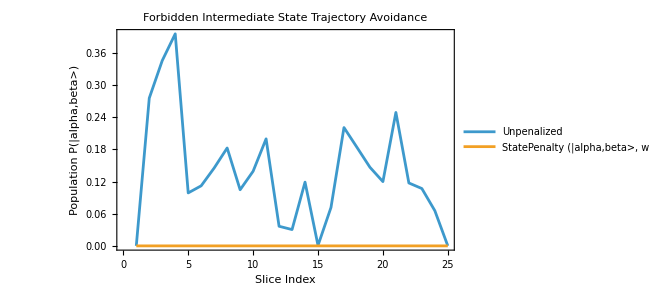

```mathematica
ListLinePlot[{trajPopNoPen, trajPopPen}, PlotLegends -> {"Unpenalized", "StatePenalty (|alpha,beta>, w=4)"},
  Frame -> True, FrameLabel -> {"Slice Index", "Population P(|alpha,beta>)"},
  PlotLabel -> "Forbidden Intermediate State Trajectory Avoidance", ImageSize -> 480]
```

### 10.2 Joint Slice Duration & Delay Optimization (OptimizeDurations, FixedTotalDuration, DelaysOnly)

OptimizeDurations computes exact analytical derivatives with respect to slice durations dt_j (including causal suffix-sum chain rules over continuous CF4 MAS drifts). Supports bounded durations (DurationBounds), fixed-total-duration simplex projection (FixedTotalDuration -> True), and "DelaysOnly" free-evolution delay refinement.

```mathematica
SetSpinSystem[{{1, 1/2}, {2, 1/2}}]; b2 = ZeemanBasis[];
probMASDur = OptimalControlProblem[Hdip, ctrls4, StateTarget[opI[1, "z"] -> opI[2, "z"]], {0.8 * trMAS, 8},
  FrequencyUnits -> "Hz", InitialTimePoint -> trMAS / 4., DriftIntegration -> "CF4", OptimizeDurations -> True];
vgMASDur = VerifyOptimalControlGradient[probMASDur, uProbe[[1 ;; 8]], StepSize -> {0.5, Automatic}];

resFixedDur = GRAPEOptimize[
  OptimalControlProblem[1500. * opI[1, "z"] - 3500. * opI[2, "z"] + 2000. * opI[1, "z"] . opI[2, "z"], ctrls4,
    StateTarget[opI[1, "z"] -> 2 opI[1, "z"] . opI[2, "z"]], {4.*^-4, 6}, FrequencyUnits -> "Hz",
    OptimizeDurations -> True, FixedTotalDuration -> True, DurationBounds -> {2.*^-5, 2.*^-4}],
  InitialControls -> 800., MaxIterations -> 120, TargetFidelity -> 0.9995, RandomSeed -> 23];
simFixedDur = VerifyOptimalControlSimulation[resFixedDur, Tolerance -> 10^-10];

echoInit = ConstantArray[0., {3, 4}]; echoInit[[1, 2]] = 5000.; echoInit[[3, 1]] = 5000.; echoInit[[3, 3]] = 5000.;
resDelays = GRAPEOptimize[
  OptimalControlProblem[1000. * opI[1, "z"] . opI[2, "z"], ctrls4, StateTarget[opI[1, "z"] -> 2 opI[1, "z"] . opI[2, "z"]],
    {5.*^-5, 0.25*^-3, 5.*^-5}, FrequencyUnits -> "Hz", OptimizeDurations -> "DelaysOnly",
    InitialControls -> echoInit, DurationBounds -> {5.*^-5, 1.5*^-3}, AmplitudeBound -> 12000.],
  MaxIterations -> 120, TargetFidelity -> 0.9999];
simDelays = VerifyOptimalControlSimulation[resDelays, Tolerance -> 10^-10];
<|
  "MAS_DurGradRelErr" -> vgMASDur["DurationMaxRelativeError"],
  "FixedDur_F" -> resFixedDur["FinalFidelity"],
  "FixedDur_SumErr" -> Abs[Total[resFixedDur["TimeSteps"]] - 4.*^-4],
  "FixedDur_SDMatch" -> simFixedDur["FidelityMatchQ"],
  "DelaysOnly_F" -> resDelays["FinalFidelity"],
  "DelaysOnly_MidDelay_us" -> 10^6 * resDelays["TimeSteps"][[2]],
  "DelaysOnly_DelayCtrlNorm" -> Norm[resDelays["Controls"][[2]]],
  "DelaysOnly_SDMatch" -> simDelays["FidelityMatchQ"]
|>
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

<|MAS_DurGradRelErr→8.38836×10^-10,FixedDur_F→0.999537,FixedDur_SumErr→1.0842×10^-19,FixedDur_SDMatch→True,DelaysOnly_F→0.999928,DelaysOnly_MidDelay_us→436.554,DelaysOnly_DelayCtrlNorm→0.,DelaysOnly_SDMatch→True|>

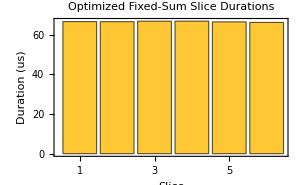
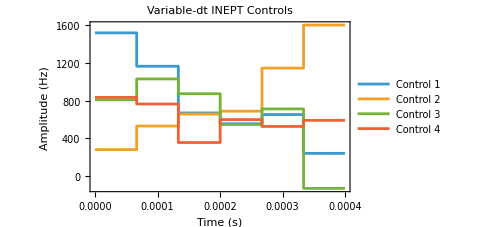

```mathematica
Row[{
  BarChart[10^6 * resFixedDur["TimeSteps"], ChartLabels -> Range[6], Frame -> True,
    FrameLabel -> {"Slice", "Duration (us)"}, PlotLabel -> "Optimized Fixed-Sum Slice Durations", ImageSize -> 300],
  PlotOptimalControlWaveform[resFixedDur, PlotLabel -> "Variable-dt INEPT Controls", ImageSize -> 370]
}]
```

## 11. Subspace Targets, Virtual-Z Phase Freedom & Hardware Export (Phase 2C)

### 11.1 Embedded Subspace Unitary Gates & Leakage Suppression (SubspaceUnitaryTarget, LeakageWeight)

SubspaceUnitaryTarget[Usub, subspace] targets a unitary transformation restricted to a k-dimensional embedded subspace (from state indices, Kets, or an orthonormal isometry matrix) while penalizing subspace population loss L(U) = 1 - Tr[W^H W]/k weighted by LeakageWeight.

```mathematica
SetSpinSystem[{{1, 1/2}, {2, 1/2}}]; b2 = ZeemanBasis[];
hadamard2 = N[{{1, 1}, {1, -1}} / Sqrt[2.]];
resSubNoLeak = GRAPEOptimize[
  OptimalControlProblem[2000. * opI[1, "z"] . opI[2, "z"], ctrls4,
    SubspaceUnitaryTarget[hadamard2, {2, 3}, PhaseFreedom -> "Diagonal", LeakageWeight -> 0.],
    {6.*^-4, 12}, FrequencyUnits -> "Hz"],
  MaxIterations -> 150, TargetFidelity -> 0.999, RandomSeed -> 51];
resSubLeak = GRAPEOptimize[
  OptimalControlProblem[2000. * opI[1, "z"] . opI[2, "z"], ctrls4,
    SubspaceUnitaryTarget[hadamard2, {2, 3}, PhaseFreedom -> "Diagonal", LeakageWeight -> 1.0],
    {6.*^-4, 12}, FrequencyUnits -> "Hz"],
  MaxIterations -> 200, TargetFidelity -> 0.999, RandomSeed -> 51];
simSubLeak = VerifyOptimalControlSimulation[resSubLeak, Tolerance -> 10^-10];
<|
  "NoPenalty" -> <|"SubspaceF" -> resSubNoLeak["Extra", "SubspaceFidelity"], "Leakage" -> resSubNoLeak["Leakage"]|>,
  "WithLeakageWeight" -> <|"SubspaceF" -> resSubLeak["Extra", "SubspaceFidelity"], "Leakage" -> resSubLeak["Leakage"], "FinalF" -> resSubLeak["FinalFidelity"], "SDMatch" -> simSubLeak["FidelityMatchQ"]|>
|>
```

SetSpinSystem::set: the spin system has been set to {{1,1/2},{2,1/2}}

<|NoPenalty→<|SubspaceF→0.999441,Leakage→0.000525671|>,WithLeakageWeight→<|SubspaceF→0.999675,Leakage→0.000323601,FinalF→0.999351,SDMatch→True|>|>

### 11.2 Parametric Virtual-Z Phase Freedom (LeftZ / RightZ / BothZ / Generators) & OptimalPhases

PhaseFreedom accepts non-parametric invariants (None, "Global", "Diagonal"/"SubspaceDiagonal") as well as smooth joint-optimized virtual rotations ("LeftZ", "RightZ", "BothZ", spin subsets, or custom Hermitian "Generators") compatible with Strong-Wolfe L-BFGS and FISTA. Here a 400 us CNOT infeasible without phase freedom converges rapidly to F > 0.9995 under "BothZ".

```mathematica
hCNOT = 2500. * opI[1, "z"] - 3500. * opI[2, "z"] + 1500. * opI[1, "z"] . opI[2, "z"];
cnotTar = {{1., 0., 0., 0.}, {0., 1., 0., 0.}, {0., 0., 0., 1.}, {0., 0., 1., 0.}};
vgPhiBothZ = VerifyOptimalControlGradient[
  OptimalControlProblem[hCNOT, ctrls4, UnitaryTarget[cnotTar, PhaseFreedom -> "BothZ"], {4.*^-4, 10}, FrequencyUnits -> "Hz"],
  Join[Flatten[ConstantArray[{200., -150., 180., 120.}, 10]], {0.31, -0.74, 1.15, -0.42}],
  StepSize -> {0.5, Automatic, 10^-5}];
pfCompare = Table[
  With[{r = GRAPEOptimize[OptimalControlProblem[hCNOT, ctrls4, UnitaryTarget[cnotTar, PhaseFreedom -> pfMode], {4.*^-4, 10}, FrequencyUnits -> "Hz"],
      MaxIterations -> 150, TargetFidelity -> 0.9995, RandomSeed -> 61]},
    pfMode -> <|"Fidelity" -> r["FinalFidelity"], "Iters" -> r["Iterations"]|>
  ],
  {pfMode, {None, "Global", "Diagonal", "LeftZ", "BothZ"}}
] // Association;
resBothZ = GRAPEOptimize[OptimalControlProblem[hCNOT, ctrls4, UnitaryTarget[cnotTar, PhaseFreedom -> "BothZ"], {4.*^-4, 10}, FrequencyUnits -> "Hz"],
  MaxIterations -> 150, TargetFidelity -> 0.9995, RandomSeed -> 61];
simBothZ = VerifyOptimalControlSimulation[resBothZ, Tolerance -> 10^-10];
iz1Mat = Normal[MatrixRepresentation[opI[1, "z"], b2]]; iz2Mat = Normal[MatrixRepresentation[opI[2, "z"], b2]];
pv = resBothZ["OptimalPhases", "Vector"];
uEffManual = (MatrixExp[I pv[[1]] iz1Mat] . MatrixExp[I pv[[2]] iz2Mat]) . simBothZ["SpinDynamicaResult"] . (MatrixExp[I pv[[3]] iz1Mat] . MatrixExp[I pv[[4]] iz2Mat]);
<|
  "PhaseGradRelErr" -> vgPhiBothZ["PhaseMaxRelativeError"],
  "ModeComparison" -> pfCompare,
  "OptimalPhases_rad" -> pv,
  "ManualPhaseFidelityDiff" -> Abs[Abs[Tr[ConjugateTranspose[cnotTar] . uEffManual]]^2 / 16. - resBothZ["FinalFidelity"]],
  "SDMatch" -> simBothZ["FidelityMatchQ"]
|>
```

<|PhaseGradRelErr→4.90647×10^-11,ModeComparison→<|None→<|Fidelity→0.706579,Iters→150|>,Global→<|Fidelity→0.998112,Iters→150|>,Diagonal→<|Fidelity→0.999583,Iters→18|>,LeftZ→<|Fidelity→0.99955,Iters→41|>,BothZ→<|Fidelity→0.999552,Iters→30|>|>,OptimalPhases_rad→{-0.0267348,-0.500171,-0.802001,-0.500171},ManualPhaseFidelityDiff→1.33227×10^-15,SDMatch→True|>

### 11.3 Simultaneous Multi-Channel PulseSequence, OptimalControlPulseTable & Bruker/SIMPSON/CSV Export

Export multi-spin / multi-channel pulses directly to native SpinDynamica simultaneous PulseSequence[spins, {Delay[totalDur, TimeDependentGeneratorFunction[...]]}], polar amplitude/phase tables via OptimalControlPulseTable, and spectrometer or simulator strings/files in "Bruker" (JCAMP-DX), "SIMPSON", and "CSV" formats (including Resample for variable-duration pulses).

```mathematica
pseq4 = OptimalControlPulseSequence[resBothZ, IncludeDrift -> True];
uSeq4 = MatrixRepresentation[NPropagationOperator[pseq4, Basis -> b2], b2];
uEv4 = MatrixRepresentation[NPropagationOperator[OptimalControlEventList[resBothZ, IncludeDrift -> True], Basis -> b2], b2];
tbl4 = OptimalControlPulseTable[resBothZ];

brkAll = ExportOptimalControlPulse[resBothZ, "Bruker", Channel -> All, Title -> "CNOT_BothZ"];
simpAll = ExportOptimalControlPulse[resBothZ, "SIMPSON", Channel -> All];
csvAll = ExportOptimalControlPulse[resBothZ, "CSV"];
brkResamp = ExportOptimalControlPulse[resFixedDur, "Bruker", Channel -> 1, Resample -> 12, Title -> "FixedDur_Resamp12"];
<|
  "PulseSequence_PropErr" -> Max[Abs[uSeq4 - uEv4]],
  "TableChannels" -> Length[tbl4["Channels"]],
  "BrukerCh1ValidQ" -> StringContainsQ[brkAll[1], "##JCAMP-DX="] && StringContainsQ[brkAll[1], "##END="],
  "SimpsonChannels" -> Length[simpAll],
  "CSVHasCh2PhaseQ" -> StringContainsQ[csvAll, "Ch2_Phase_Deg"],
  "ResampledBruker12Q" -> StringContainsQ[brkResamp, "##NPOINTS= 12"],
  "CSVHeader" -> First[StringSplit[csvAll, "\n"]]
|>
```

<|PulseSequence_PropErr→9.39189×10^-16,TableChannels→2,BrukerCh1ValidQ→True,SimpsonChannels→2,CSVHasCh2PhaseQ→True,ResampledBruker12Q→True,CSVHeader→Slice,TimeStart_s,TimeEnd_s,TimeMid_s,Duration_s,Ch1_Ux_Hz,Ch1_Uy_Hz,Ch1_Amp_Hz,Ch1_Amp_Pct,Ch1_Phase_Deg,Ch2_Ux_Hz,Ch2_Uy_Hz,Ch2_Amp_Hz,Ch2_Amp_Pct,Ch2_Phase_Deg|>

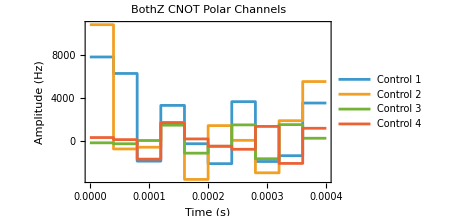
-Graphics-tMid (s) | dt (s) | Ch1 (%) | Ch1 (deg) | Ch2 (%) | Ch2 (deg)
1/50000 | 1/25000 | 100 | 2167429/40000 | 6795697/500000 | 31294379/250000
3/50000 | 1/25000 | 23672577/500000 | 176471649/500000 | 11804049/1000000 | 40460609/250000
1/10000 | 1/25000 | 3011213/200000 | 197774261/1000000 | 4150211/62500 | 270395917/1000000
7/50000 | 1/25000 | 6923349/250000 | 1356337/50000 | 85218249/1000000 | 12326981/250000
9/50000 | 1/25000 | 1088489/40000 | 33178519/125000 | 709588/15625 | 172177387/1000000

```mathematica
Row[{
  PlotOptimalControlWaveform[resBothZ, Method -> "AmplitudePhase", PlotLabel -> "BothZ CNOT Polar Channels", ImageSize -> 350],
  Grid[Prepend[Round[Take[tbl4["Table"], 5], 10^-6], {"tMid (s)", "dt (s)", "Ch1 (%)", "Ch1 (deg)", "Ch2 (%)", "Ch2 (deg)"}],
    Frame -> All, Spacings -> {1, 0.7}]
}]
```